# Rigid bodies, plastic impact

```mathematica
param={l1->2,l2->10,m1->2,m2->10,mb->40,mO->15,r->0.2,α->0.5,ρ1->1,ρ2->1,EI1->1000,EI2->1000};
beta={β1->((ω1^2ρ1)/(EI1))^1/4,β2->((ω2^2ρ2)/(EI2))^1/4};
```

```mathematica
θ00=π/2;q10=0;q20=π/2;xb0=4;yb0=2;
```

```mathematica
paramScheme={θ0[t]->θ00,q1[t]->q10,q2[t]->q20,xb[t]->xb0,yb[t]->yb0};
EulerBernoulli={v1[x,t]->B1[x]Q1[t],Derivative[1,0][v1][x,t]->B1'[x]Q1[t],Derivative[0,1][v1][x,t]->B1[x]Q1'[t],Derivative[1,1][v1][x,t]->B1'[x]Q1'[t],v2[x,t]->B2[x]Q2[t],Derivative[1,0][v2][x,t]->B2'[x]Q2[t],Derivative[0,1][v2][x,t]->B2[x]Q2'[t],Derivative[1,1][v2][x,t]->B2'[x]Q2'[t]};
Jxb=1/4 mb r^2;
Jyb=1/4 mb r^2;
Jzb=0;
Jx1=1/3m1 l1^2;
Jx2=1/3 m2 l2^2;
Jb=1/2mb r^2;
J1=1/12m1 l1^2;
J2=1/12m2 l2^2;
Jz=1/2mO r^2;
```

## Kinematics

## Manipulator

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

```mathematica
elasticMatrix[rx_,ry_,rz_,px_,py_,pz_]:={{1,-rz,ry,px},{rz,1,-rx,py},{-ry,rx,1,pz},{0,0,0,1}};
```

```mathematica
Mfb=Mrotztrasl[0,{xb[t],yb[t],0}];
```

```mathematica
Mb0=Mrotztrasl[θ0[t],{0,0,0}];
```

```mathematica
Mf0=Mfb.Mb0;Mf0//MatrixForm
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | xb[t]
Sin[θ0[t]] | Cos[θ0[t]] | 0 | yb[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[q1[t],{l1 Cos[q1[t]],l1 Sin[q1[t]],0}];M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | l1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | l1 Sin[q1[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

We will write the local deformation along the y-axis as v(x,t)=B(x)T(t)

```mathematica
E01=Mrotztrasl[D[v1[x,t],x],{0,v1[x,t],0}];E01//MatrixForm
```

(Cos[v1^(1,0)[x,t]] | -Sin[v1^(1,0)[x,t]] | 0 | 0
Sin[v1^(1,0)[x,t]] | Cos[v1^(1,0)[x,t]] | 0 | v1[x,t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*E01=elasticMatrix[0,0,D[B1[x],x]T1[t],0,B1[x]T1[t],0];E01//MatrixForm*)
```

```mathematica
T01=M01.E01;T01//MatrixForm
```

(Cos[q1[t]] Cos[v1^(1,0)[x,t]]-Sin[q1[t]] Sin[v1^(1,0)[x,t]] | -Cos[v1^(1,0)[x,t]] Sin[q1[t]]-Cos[q1[t]] Sin[v1^(1,0)[x,t]] | 0 | l1 Cos[q1[t]]-Sin[q1[t]] v1[x,t]
Cos[v1^(1,0)[x,t]] Sin[q1[t]]+Cos[q1[t]] Sin[v1^(1,0)[x,t]] | Cos[q1[t]] Cos[v1^(1,0)[x,t]]-Sin[q1[t]] Sin[v1^(1,0)[x,t]] | 0 | l1 Sin[q1[t]]+Cos[q1[t]] v1[x,t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[q2[t],{l2 Cos[q2[t]],l2 Sin[q2[t]],0}];M12//MatrixForm
```

(Cos[q2[t]] | -Sin[q2[t]] | 0 | l2 Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | l2 Sin[q2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
E12=Mrotztrasl[D[v2[x,t],x],{0,v2[x,t],0}];E12//MatrixForm
```

(Cos[v2^(1,0)[x,t]] | -Sin[v2^(1,0)[x,t]] | 0 | 0
Sin[v2^(1,0)[x,t]] | Cos[v2^(1,0)[x,t]] | 0 | v2[x,t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*E12=elasticMatrix[0,0,D[B2[x],x]T2[t],0,B2[x]T2[t],0]*);
```

```mathematica
T12=Simplify[M12.E12];
```

```mathematica
T02=Simplify[T01.T12];
```

```mathematica
Mf1=Simplify[Mf0.M01];
```

```mathematica
Mf2=Simplify[Mf1.M12];
```

```mathematica
Tf1=Simplify[Mf0.T01];
```

```mathematica
Tf2=Simplify[Tf1.T12];
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
Ob=Mfb.origin;Ob//MatrixForm
```

(xb[t]
yb[t]
0
1)

```mathematica
O1=Tf1.origin;
```

```mathematica
EE=Simplify[Tf2.origin];
```

Jacobian matrixOb:

```mathematica
J=FullSimplify[D[EE[[1;;2]],{{xb[t],yb[t],θ0[t],q1[t],q2[t],T1[t],T2[t]}}]];
```

```mathematica
J. D[{xb[t],yb[t],θ0[t],q1[t],q2[t],T1[t],T2[t]},t]==D[EE[[1;;2]],t]//Simplify
```

{Sin[q1[t]+θ0[t]] v1^(0,1)[x,t]+Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x,t]] v2^(0,1)[x,t]+(l2 Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x,t]]+Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x,t]] v2[x,t]) v1^(1,1)[x,t],-Cos[q1[t]+θ0[t]] v1^(0,1)[x,t]-Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x,t]] v2^(0,1)[x,t]+(-l2 Cos[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x,t]]+Sin[q1[t]+q2[t]+θ0[t]+v1^(1,0)[x,t]] v2[x,t]) v1^(1,1)[x,t]}=={0,0}

## Object

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: xb, yOb, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocityOb of the dof and the contact point:

```mathematica
MfO0=Mrotztrasl[0,{xO[t],yO[t],0}];MfO0//MatrixForm
```

(1 | 0 | 0 | xO[t]
0 | 1 | 0 | yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO0O1=Mrotztrasl[Ω[t],{0,0,0}];MO0O1//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO1O2=Mrotztrasl[α,{r Cos[α] ,r Sin[α],0}];MO1O2//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | r Cos[α]
Sin[α] | Cos[α] | 0 | r Sin[α]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MfO1=MfO0.MO0O1;
MfO2=Simplify[MfO0.MO0O1.MO1O2];MfO2//MatrixForm
```

(Cos[α+Ω[t]] | -Sin[α+Ω[t]] | 0 | r Cos[α+Ω[t]]+xO[t]
Sin[α+Ω[t]] | Cos[α+Ω[t]] | 0 | r Sin[α+Ω[t]]+yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactP=(MfO2.{0,0,0,1})[[1;;2]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[α+Ω[t]]+xO[t]
r Sin[α+Ω[t]]+yO[t])

(xO'[t]-r Sin[α+Ω[t]] Ω'[t]
yO'[t]+r Cos[α+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{xO[t],yO[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[α+Ω[t]]
0 | 1 | r Cos[α+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[α+Ω[t]] | r Cos[α+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

## Beam Theory

## Link 1

```mathematica
ML1=m2+mO;
JL1=J1+Jz+mO l2^2;
```

```mathematica
B1[x_]:=C1( Cos[β1 x]- Cosh[β1 x]+ν1(Sin[β1 x]-Sinh[β1 x]));
```

```mathematica
freqEq1=(1+Cos[β1 l1]Cosh[β1 l1])-(ML1 β1/ρ1)(Sin[β1 l1]Cosh[β1 l1]-Cos[β1 l1]Sinh[β1 l1])-(JL1 β1^3/ρ1)(Sin[β1 l1]Cosh[β1 l1]+Cos[β1 l1]Sinh[β1 l1])+(ML1 JL1 β1^4/ρ1^2)(1-Cos[β1 l1]Cosh[β1 l1]);
```

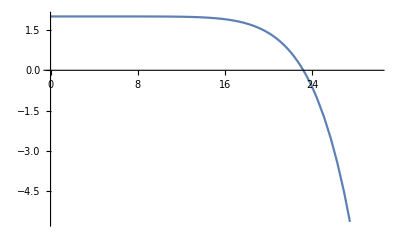

```mathematica
Plot[Simplify[(freqEq1/.beta/.param)],{ω1,0,30}]
```

```mathematica
freq1=FindRoot[(freqEq1/.beta/.param),{ω1,20,25}][[1,2]]
```

23.1974

```mathematica
const1=Simplify[Solve[Integrate[B1[x]^2,{x,0,l1}]==1,C1]][[2,1,2]];
```

```mathematica
ν1=(Sin[β1 l1]-Sinh[β1 l1]+ML1/ρ1(Cos[β1 l1]-Cosh[β1 l1]))/(Cos[β1 l1]+Cosh[β1 l1]-ML1/ρ1(Sin[β1 l1]-Sinh[β1 l1]));
```

## Link 2

```mathematica
ML2=mO;
JL2=Jz;
```

```mathematica
B2[x_]:=C2( Cos[β2 x]- Cosh[β2 x]+ν2(Sin[β2 x]-Sinh[β2 x]));
```

```mathematica
freqEq2=(1+Cos[β2 l2]Cosh[β2 l2])-(ML2 β2/ρ2)(Sin[β2 l2]Cosh[β2 l2]-Cos[β2 l2]Sinh[β2 l2])-(JL2 β2^3/ρ2)(Sin[β2 l2]Cosh[β2 l2]+Cos[β2 l2]Sinh[β2 l2])+(ML2 JL2 β2^4/ρ2^2)(1-Cos[β2 l2]Cosh[β2 l2]);
```

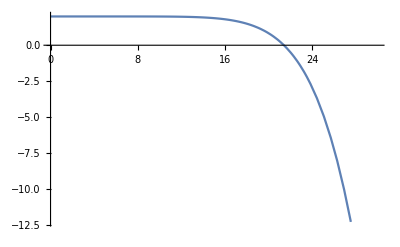

```mathematica
Plot[Simplify[(freqEq2/.beta/.param)],{ω2,0,30}]
```

```mathematica
freq2=FindRoot[(freqEq2/.beta/.param),{ω2,20,25}][[1,2]]
```

21.4134

```mathematica
const2=Simplify[Solve[Integrate[B2[x]^2,{x,0,l2}]==1,C2]][[2,1,2]];
```

```mathematica
ν2=(Sin[β2 l2]-Sinh[β2 l2]+ML2/ρ2(Cos[β2 l2]-Cosh[β2 l2]))/(Cos[β2 l2]+Cosh[β2 l2]-ML2/ρ2(Sin[β2 l2]-Sinh[β2 l2]));
```

## Dynamics

## Manipulator

### IR method

```mathematica
smallAngles={Derivative[1,0][v1][x,t]->0,Derivative[1,0][v2][x,t]->0};
```

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

Inertia frame in the com of the round base:

```mathematica
J00={{Jxb,0,0,0},{0,Jyb,0,0},{0,0,Jzb,0},{0,0,0,mb}};J00//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J0f=Simplify[Mf0.J00.Transpose[Mf0]];J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
J11={{Jx1,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J11//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J1f=Simplify[Tf1.J11.Transpose[Tf1]];
```

```mathematica
J22={{Jx2,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J22//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J2f=Simplify[Tf2.J22.Transpose[Tf2]];
```

```mathematica
Wf0=Simplify[D[Mf0,t].Inverse[Mf0]];Wf0//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb=Simplify[D[Mfb,t].Inverse[Mfb]];Wfb//MatrixForm
```

(0 | 0 | 0 | xb'[t]
0 | 0 | 0 | yb'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0=Simplify[D[Mb0,t].Inverse[Mb0]];Wb0//MatrixForm
```

(0 | -θ0'[t] | 0 | 0
θ0'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0Ff=Simplify[Mfb.Wb0.Inverse[Mfb]];Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | yb[t] θ0'[t]
θ0'[t] | 0 | 0 | -xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb+Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Lfbx=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Lfby=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Lb0=Wb0/θ0'[t];
```

```mathematica
Lb0Ff=Simplify[Mf0.Lb0.Inverse[Mf0]];Lb0Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WT01=FullSimplify[D[T01,t].Inverse[T01]/.smallAngles];WT01//MatrixForm
```

(0 | -q1'[t]-v1^(1,1)[x,t] | 0 | -Sin[q1[t]] v1^(0,1)[x,t]+(l1 Sin[q1[t]]+Cos[q1[t]] v1[x,t]) v1^(1,1)[x,t]
q1'[t]+v1^(1,1)[x,t] | 0 | 0 | Cos[q1[t]] v1^(0,1)[x,t]+(-l1 Cos[q1[t]]+Sin[q1[t]] v1[x,t]) v1^(1,1)[x,t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01=FullSimplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -q1'[t] | 0 | 0
q1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

The diagonal contributions appear to be non zero. This is because we have assumed the angle so small that the cosine is 1 and the sine is zero. By assuming again T(t)B’(x)≈0, the diagonal becomes zero and the velocity becomes q1’(t)+B1(x)’T1(t)’.
We also want just W01 since we need L01: we suppose that no forces act on the flexible coordinates, so no motion is enable by them.

```mathematica
L01=W01/q1'[t];
```

```mathematica
L01Ff=Simplify[Mf0.L01.Inverse[Mf0]];L01Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WTf1=FullSimplify[D[Tf1,t].Inverse[Tf1]];WTf1//MatrixForm
```

(0 | -q1'[t]-θ0'[t]-v1^(1,1)[x,t] | 0 | yb[t] q1'[t]+xb'[t]+yb[t] θ0'[t]-Sin[q1[t]+θ0[t]] v1^(0,1)[x,t]+(l1 Sin[q1[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x,t]+yb[t]) v1^(1,1)[x,t]
q1'[t]+θ0'[t]+v1^(1,1)[x,t] | 0 | 0 | yb'[t]+Cos[q1[t]+θ0[t]] v1^(0,1)[x,t]+(-l1 Cos[q1[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x,t]) v1^(1,1)[x,t]-xb[t] (q1'[t]+θ0'[t]+v1^(1,1)[x,t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf1=Simplify[D[Mf1,t].Inverse[Mf1]];
```

```mathematica
WT12=FullSimplify[D[T12,t].Inverse[T12]];WT12//MatrixForm
```

(0 | -q2'[t]-v2^(1,1)[x,t] | 0 | -Sin[q2[t]] v2^(0,1)[x,t]+(l2 Sin[q2[t]]+Cos[q2[t]] v2[x,t]) v2^(1,1)[x,t]
q2'[t]+v2^(1,1)[x,t] | 0 | 0 | Cos[q2[t]] v2^(0,1)[x,t]+(-l2 Cos[q2[t]]+Sin[q2[t]] v2[x,t]) v2^(1,1)[x,t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];
```

```mathematica
L12=W12/q2'[t];
L12Ff=Simplify[Mf1.L12.Inverse[Mf1]];L12Ff//MatrixForm
```

(0 | -1 | 0 | l1 Sin[q1[t]+θ0[t]]+yb[t]
1 | 0 | 0 | -l1 Cos[q1[t]+θ0[t]]-xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WTf2=FullSimplify[D[Tf2,t].Inverse[Tf2]/.smallAngles];WTf2//MatrixForm
```

(0 | -q1'[t]-q2'[t]-θ0'[t]-v1^(1,1)[x,t]-v2^(1,1)[x,t] | 0 | (l1 Sin[q1[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x,t]) q2'[t]+xb'[t]-Sin[q1[t]+θ0[t]] v1^(0,1)[x,t]-Sin[q1[t]+q2[t]+θ0[t]] v2^(0,1)[x,t]+(l1 Sin[q1[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x,t]) v1^(1,1)[x,t]+(l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]]+Cos[q1[t]+θ0[t]] v1[x,t]+Cos[q1[t]+q2[t]+θ0[t]] v2[x,t]) v2^(1,1)[x,t]+yb[t] (q1'[t]+q2'[t]+θ0'[t]+v1^(1,1)[x,t]+v2^(1,1)[x,t])
q1'[t]+q2'[t]+θ0'[t]+v1^(1,1)[x,t]+v2^(1,1)[x,t] | 0 | 0 | (-l1 Cos[q1[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x,t]) q2'[t]+yb'[t]+Cos[q1[t]+θ0[t]] v1^(0,1)[x,t]+Cos[q1[t]+q2[t]+θ0[t]] v2^(0,1)[x,t]+(-l1 Cos[q1[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x,t]) v1^(1,1)[x,t]+(-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]]+Sin[q1[t]+θ0[t]] v1[x,t]+Sin[q1[t]+q2[t]+θ0[t]] v2[x,t]) v2^(1,1)[x,t]-xb[t] (q1'[t]+q2'[t]+θ0'[t]+v1^(1,1)[x,t]+v2^(1,1)[x,t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf2=Simplify[D[Mf2,t].Inverse[Mf2]];
```

Now we also have potential energy, due to the stiffness of the flexible links:

```mathematica
v1[x,t]/.EulerBernoulli
```

C1 Q1[t] (Cos[x β1]-Cosh[x β1]+((((m2+mO) (Cos[l1 β1]-Cosh[l1 β1]))/ρ1+Sin[l1 β1]-Sinh[l1 β1]) (Sin[x β1]-Sinh[x β1]))/(Cos[l1 β1]+Cosh[l1 β1]-((m2+mO) (Sin[l1 β1]-Sinh[l1 β1]))/ρ1))

```mathematica
Simplify@B1[x]
```

C1 (Cos[x β1]-Cosh[x β1]+((((m2+mO) (Cos[l1 β1]-Cosh[l1 β1]))/ρ1+Sin[l1 β1]-Sinh[l1 β1]) (Sin[x β1]-Sinh[x β1]))/(Cos[l1 β1]+Cosh[l1 β1]-((m2+mO) (Sin[l1 β1]-Sinh[l1 β1]))/ρ1))

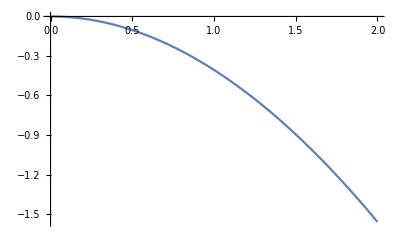

```mathematica
Plot[Simplify[B1[x]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.param/.ω1->freq1],{x,0,l1/.param}]
```

```mathematica
Simplify[D[v1[x,t]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.param/.ω1->freq1,x,x]^2]
```

0.177854 Q1[t]^2 (1. Cos[0.13453 x]+1. Cosh[0.13453 x]-0.839827 Sin[0.13453 x]-0.839827 Sinh[0.13453 x])^2

```mathematica
U1=Simplify[1/2Integrate[EI1 D[v1[x,t]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.param,x,x]^2,{x,0,l1}]]/.param;
U2=Simplify[1/2Integrate[EI2 D[v2[x,t]/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.param,x,x]^2,{x,0,l2}]]/.param;
```

```mathematica
K1=Simplify[1/2Tr[Wf0.J0f.Transpose[Wf0]]/.smallAngles];
K2=Simplify[1/2Tr[WTf1.J1f.Transpose[WTf1]]/.smallAngles];
K3=Simplify[1/2Tr[WTf2.J2f.Transpose[WTf2]]/.smallAngles];
```

```mathematica
Ktot=(K1+K2+K3)/.EulerBernoulli/.{C1->const1,C2->const2}/.beta/.x->l1/.param;
Utot=U1+U2;
```

```mathematica
L=Ktot-Utot;
```

By neglecting the constraints forces (since they don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ0b=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ0b//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕbf=FullSimplify[Mf0.ϕ0b.Transpose[Mf0]];
```

```mathematica
ϕ11=actionMatrix[0,0,τ2-τ3,0,0,0];ϕ11//MatrixForm
ϕ1f=FullSimplify[Mf1.ϕ11.Transpose[Mf1]];ϕ1f//MatrixForm
```

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ϕ22=actionMatrix[0,0,τ3,0,0,0];
ϕ2f=FullSimplify[Mf2.ϕ22.Transpose[Mf2]];
```

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfbx]]
f2=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfby]]
f3=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lb0Ff]]
f4=FullSimplify[PSS[(ϕ1f+ϕ2f),L01Ff]]
f5=Simplify[PSS[(ϕ2f),L12Ff]]
```

Fx Cos[θ0[t]]-Fy Sin[θ0[t]]

Fy Cos[θ0[t]]+Fx Sin[θ0[t]]

τ1

τ2

τ3

```mathematica
eq1=D[D[L,xb'[t]],t]-D[L,xb[t]]-f1;
eq2=D[D[L,yb'[t]],t]-D[L,yb[t]]-f2;
eq3=D[D[L,θ0'[t]],t]-D[L,θ0[t]]-f3;
eq4=D[D[L,q1'[t]],t]-D[L,q1[t]]-f4;
eq5=D[D[L,q2'[t]],t]-D[L,q2[t]]-f5;
eq6=D[D[L,Q1'[t]],t]-D[L,Q1[t]]-0;
eq7=D[D[L,Q2'[t]],t]-D[L,Q2[t]]-0;
```

```mathematica
{c,A}=Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5,eq6,eq7},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Q1''[t],Q2''[t],Fx,Fy,τ1,τ2,τ3}];
```

```mathematica
M=A[[1;;7,1;;7]];
u=-A[[1;;7,8;;12]];
```

```mathematica
freq1
```

23.1974

```mathematica
freq2
```

21.4134

### Classic Lagrangian method

```mathematica
Ob2D=(Mfb.{0,0,0,1})[[1;;2]];
O12D=Simplify[(Tf1.{-l1/2,0,0,1})[[1;;2]]];
EE2D=Simplify[(Tf2.{-l2/2,0,0,1})[[1;;2]]];
```

```mathematica
Vb=D[Ob2D,t];
V1=D[O12D,t];
V2=D[EE2D,t];
```

```mathematica
FullSimplify[Expand[(Simplify[V1]-(Simplify[WTf1.O1])[[1;;2]])]]/.param/.paramScheme/.{v1[x,t]->1.,Derivative[1,0][v1][x,t]->1.,Derivative[0,1][v1][x,t]->1.,Derivative[1,1][v1][x,t]->1.,v2[x,t]->1.,Derivative[1,0][v2][x,t]->1.,Derivative[0,1][v2][x,t]->1.,Derivative[1,1][v2][x,t]->1.}
```

{1/2 (0.+0.270151 (1.+q1'[t]+θ0'[t])-2 (1.+WTf1.{3.,2.5,0,1}-xb'[t]+0.5 (q1'[t]+θ0'[t]))),0.210368-WTf1.{3.,2.5,0,1}-0.789632 q1'[t]+yb'[t]-0.789632 θ0'[t]}

```mathematica
vbsquare=Simplify[Vb[[1]]^2+Vb[[2]]^2];
v1square=Simplify[V1[[1]]^2+V1[[2]]^2];
v2square=Simplify[V2[[1]]^2+V2[[2]]^2];
```

Inertia wrt CoM:

```mathematica
tb=Simplify[1/2mb vbsquare+1/2Ib (θ0'[t])^2/.smallAngles];
t1=Simplify[1/2m1 v1square+1/2I1 (θ0'[t]+q1'[t]+Derivative[1,1][v1][x,t])^2/.smallAngles];
t2=Simplify[1/2m2 v2square+1/2I2 (θ0'[t]+q1'[t]+Derivative[1,1][v1][x,t]+q2'[t]+Derivative[1,1][v2][x,t])^2/.smallAngles];
```

```mathematica
Expand@t2/.param/.paramScheme/.{v1[x,t]->2,Derivative[1,0][v1][x,t]->1,Derivative[0,1][v1][x,t]->2,Derivative[1,1][v1][x,t]->1,v2[x,t]->2,Derivative[1,0][v2][x,t]->1,Derivative[0,1][v2][x,t]->2,Derivative[1,1][v2][x,t]->1}
Expand@K3/.param/.paramScheme/.{v1[x,t]->2,Derivative[1,0][v1][x,t]->1,Derivative[0,1][v1][x,t]->2,Derivative[1,1][v1][x,t]->1,v2[x,t]->2,Derivative[1,0][v2][x,t]->1,Derivative[0,1][v2][x,t]->2,Derivative[1,1][v2][x,t]->1}
```

120.417+330.417 q1'[t]+250.417 q1'[t]^2+130.417 q2'[t]+190.833 q1'[t] q2'[t]+40.4167 q2'[t]^2-40. xb'[t]-57.5 q1'[t] xb'[t]-17.5 q2'[t] xb'[t]+5 xb'[t]^2-20 yb'[t]-40 q1'[t] yb'[t]-20 q2'[t] yb'[t]+5 yb'[t]^2+330.417 θ0'[t]+500.833 q1'[t] θ0'[t]+190.833 q2'[t] θ0'[t]-57.5 xb'[t] θ0'[t]-40 yb'[t] θ0'[t]+250.417 θ0'[t]^2

120.417+330.417 q1'[t]+250.417 q1'[t]^2+130.417 q2'[t]+190.833 q1'[t] q2'[t]+40.4167 q2'[t]^2-40. xb'[t]-57.5 q1'[t] xb'[t]-17.5 q2'[t] xb'[t]+5 xb'[t]^2-20 yb'[t]-40 q1'[t] yb'[t]-20 q2'[t] yb'[t]+5 yb'[t]^2+330.417 θ0'[t]+500.833 q1'[t] θ0'[t]+190.833 q2'[t] θ0'[t]-57.5 xb'[t] θ0'[t]-40 yb'[t] θ0'[t]+250.417 θ0'[t]^2

```mathematica
lmid=(tb+t1+t2)/.EulerBernoulli;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,xb'[t]],t]-D[lmid,xb[t]]-f1];
eq2Mid=Simplify[D[D[lmid,yb'[t]],t]-D[lmid,yb[t]]-f2];
eq3Mid=Simplify[D[D[lmid,θ0'[t]],t]-D[lmid,θ0[t]]-f3];
eq4Mid=Simplify[D[D[lmid,q1'[t]],t]-D[lmid,q1[t]]-f4];
eq5Mid=Simplify[D[D[lmid,q2'[t]],t]-D[lmid,q2[t]]-f5];
eq6Mid=Simplify[D[D[lmid,Q1'[t]],t]-D[lmid,Q1[t]]-0];
eq7Mid=Simplify[D[D[lmid,Q2'[t]],t]-D[lmid,Q2[t]]-0];
```

```mathematica
{c2,A2}=Normal@CoefficientArrays[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid,eq6Mid,eq7Mid},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Q1''[t],Q2''[t],Fx,Fy,τ1,τ2,τ3}];
M2=Simplify@A2[[1;;7,1;;7]];
u2=-A2[[1;;7,8;;12]];
```

```mathematica
FullSimplify[c2[[1]]==c[[1]]]
FullSimplify[c2[[2]]==c[[2]]]
FullSimplify[c2[[3]]==c[[3]]]
FullSimplify[c2[[4]]==c[[4]]]
FullSimplify[c2[[5]]==c[[5]]]
FullSimplify[c2[[6]]==c[[6]]]
FullSimplify[c2[[7]]==c[[7]]]
```

True

True

True

«4 more identical outputs»

```mathematica
FullSimplify[M[[1]]==M2[[1]]]
FullSimplify[M[[2]]==M2[[2]]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
FullSimplify[M[[6]]==M2[[6]]]
FullSimplify[M[[7]]==M2[[7]]]
```

True

True

True

«4 more identical outputs»

## Object

### IR method

```mathematica
IxO=1/4 mO r^2;
IyO=1/4 mO r^2;
IzO=0;
```

```mathematica
JO1O1={{IxO,0,0,0},{0,IyO,0,0},{0,0,IzO,0},{0,0,0,mO}};JO1O1//MatrixForm
```

((mO r^2)/4 | 0 | 0 | 0
0 | (mO r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mO)

```mathematica
J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
JOf=Simplify[MfO1.JO1O1.Transpose[MfO1]];JOf//MatrixForm
```

(1/4 mO (r^2+4 xO[t]^2) | mO xO[t] yO[t] | 0 | mO xO[t]
mO xO[t] yO[t] | 1/4 mO (r^2+4 yO[t]^2) | 0 | mO yO[t]
0 | 0 | 0 | 0
mO xO[t] | mO yO[t] | 0 | mO)

```mathematica
WfO1=Simplify[D[MfO1,t].Inverse[MfO1]];WfO1//MatrixForm
```

(0 | -Ω'[t] | 0 | xO'[t]+yO[t] Ω'[t]
Ω'[t] | 0 | 0 | yO'[t]-xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1=Simplify[D[MO0O1,t].Inverse[MO0O1]];WO0O1//MatrixForm
```

(0 | -Ω'[t] | 0 | 0
Ω'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1Ff=FullSimplify[MfO0.WO0O1.Inverse[MfO0]];WO0O1Ff//MatrixForm
```

(0 | -Ω'[t] | 0 | yO[t] Ω'[t]
Ω'[t] | 0 | 0 | -xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LO0O1Ff=Simplify[WO0O1Ff/Ω'[t]];LO0O1Ff//MatrixForm
```

(0 | -1 | 0 | yO[t]
1 | 0 | 0 | -xO[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LfOx=Lfbx;
LfOy=Lfby;
```

```mathematica
ϕO1O1=actionMatrix[0,0,τO,FOx,FOy,0];
ϕO1O1Ff=FullSimplify[MfO1.ϕO1O1.Transpose[MfO1]];
```

```mathematica
f1O=FullSimplify[PSS[ϕO1O1Ff,LfOx]]
f2O=FullSimplify[PSS[ϕO1O1Ff,LfOy]]
f3O=FullSimplify[PSS[ϕO1O1Ff,LO0O1Ff]]
```

FOx Cos[Ω[t]]-FOy Sin[Ω[t]]

FOy Cos[Ω[t]]+FOx Sin[Ω[t]]

τO

```mathematica
TO=Simplify[1/2Tr[WfO1.JOf.Transpose[WfO1]]];
LO=TO;
```

```mathematica
eq1OIR=Simplify[D[D[LO,xO'[t]],t]-D[L,xO[t]]-f1O];
eq2OIR=Simplify[D[D[LO,yO'[t]],t]-D[L,yO[t]]-f2O];
eq3OIR=Simplify[D[D[LO,Ω'[t]],t]-D[L,Ω[t]]-f3O];
```

```mathematica
{co,Ao}=FullSimplify[Normal@CoefficientArrays[{eq1OIR,eq2OIR,eq3OIR},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}]];
Mo=Ao[[1;;3,1;;3]];
uo=-Ao[[1;;3,4;;6]];
```

```mathematica
Mo//MatrixForm
co//MatrixForm
uo//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

### Classic method

```mathematica
T=1/2 mO(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1O=Simplify[D[D[T,xO'[t]],t]-D[T,xO[t]]-f1O];
eq2O=Simplify[D[D[T,yO'[t]],t]-D[T,yO[t]]-f2O];
eq3O=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-f3O];
```

```mathematica
{co2,Ao2}=Normal@CoefficientArrays[{eq1O,eq2O,eq3O},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}];
Mo2=Ao2[[1;;3,1;;3]];
uo2=-Ao2[[1;;3,4;;6]];
```

```mathematica
Mo2//MatrixForm
co2//MatrixForm
uo2//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Jo//MatrixForm
```

```mathematica
({{1, 0, -r Sin[α+Ω[t]]}, {0, 1, r Cos[α+Ω[t]]}})
```

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=Transpose[Jo].Inverse[Jo.Transpose[Jo]]//Simplify;pseudoInverseJo//MatrixForm
```

```mathematica
({{(2+r^2+r^2 Cos[2 (α+Ω[t])])/(2 (1+r^2)), (r^2 Cos[α+Ω[t]] Sin[α+Ω[t]])/(1+r^2)}, {(r^2 Cos[α+Ω[t]] Sin[α+Ω[t]])/(1+r^2), (2+r^2-r^2 Cos[2 (α+Ω[t])])/(2 (1+r^2))}, {-(r Sin[α+Ω[t]])/(1+r^2), (r Cos[α+Ω[t]])/(1+r^2)}})
```

```mathematica
G=M+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J//FullSimplify ;
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t]};
p'=D[p,t];
```

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
H=M. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'//Simplify;
```

```mathematica
Det[G]
```

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
pf'=Inverse[G].H ;
```

Final values of the satellite after the impact:

```mathematica
ψf'=pseudoInverseJo.J.pf';
```

### Initial conditions

After the capture, we assume that the object is now perfectlyOb attached to the EE, hence the contact point’s variables coincides with the ones of the EE. We also assume that the spinning velocityOb is resetted:

```mathematica
EEi=EE[[1;;2]]/.param/.paramScheme
```

{4.,9.5}

Condition for alignment of the object with the EE:

```mathematica
contactCondition=(θ00+q10+q20+π-(α/.param))
```

4.21239

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{-1.83697×10^-16+xO[t],-1.+yO[t]}

```mathematica
objectPosI=(Solve[{EEi[[1]]==(contactP/.param/.Ω[t]->contactCondition)[[1]],EEi[[2]]==(contactP/.param/.Ω[t]->contactCondition)[[2]]},{xO[t],yO[t]}])[[1]]
```

{xO[t]→4.,yO[t]→10.5}

Let’s suppose initial zero velocities of the BM syObstem.

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→0,xb[t]→4,yb[t]→2}

```mathematica
initialConditions1={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->-1,yO'[t]->0,Ω'[t]->0};
initialConditions2={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->0,yO'[t]->-1,Ω'[t]->0};
```

```mathematica
pf1'=pf'/.initialConditions1/.param/.paramScheme
pf2'=pf'/.initialConditions2/.param/.paramScheme
```

{-0.00355556,-8.61788×10^-19,2.80549×10^-15,-0.056,0.369905}

{2.89096×10^-18,-0.111111,3.73925×10^-31,1.06111×10^-17,7.51712×10^-18}

```mathematica
ψf1'=ψf'/.initialConditions1/.param/.paramScheme
ψf2'=ψf'/.initialConditions2/.param/.paramScheme
```

{-0.439111,-8.15252×10^-17,-0.439111}

{-6.17063×10^-17,-0.111111,-4.12955×10^-17}

```mathematica
a=((Jo.ψf')/.initialConditions1/.param/.paramScheme)
```

{-0.878222,-8.61788×10^-19}

```mathematica
b=((J.pf')/.initialConditions1/.param/.paramScheme)
```

{-0.878222,-8.61788×10^-19}

```mathematica
a-b
```

{0.,-1.96445×10^-32}

## Post-impact

-Graphics-

```mathematica
EEp=EE[[1;;2]]/.param;
```

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{-1.83697×10^-16+xO[t],-1.+yO[t]}

```mathematica
contactConditionP=(θ0[t]+q1[t]+q2[t]+π-(α/.param));
```

```mathematica
objectPosP=(Solve[{EE[[1]]==(contactP/.param/.Ω[t]->contactConditionP)[[1]],EE[[2]]==(contactP/.param/.Ω[t]->contactConditionP)[[2]]},{xO[t],yO[t]}])[[1]];
```

```mathematica
ψp={objectPosP[[1,2]],objectPosP[[2,2]],contactConditionP};
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]}
```

{xO[t]→-1. (-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]]+1. Cos[3.14159+q1[t]+q2[t]+θ0[t]]-xb[t]),yO[t]→-1. (-l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]]+1. Sin[3.14159+q1[t]+q2[t]+θ0[t]]-yb[t]),Ω[t]→2.64159+q1[t]+q2[t]+θ0[t]}

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

Since we are considering only rigid bodies, there is no contribution of the elastic part (no matrix K).

```mathematica
Mp=M+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp;
```

```mathematica
Dimensions[eqMotion]
```

{5}

### Simulation with no control

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→0,xb[t]→4,yb[t]→2}

```mathematica
NDinitialCondition1={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf1'[[1]],yb'[0]==pf1'[[2]],θ0'[0]==pf1'[[3]],q1'[0]==pf1'[[4]],q2'[0]==pf1'[[5]]};
NDinitialCondition2={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf2'[[1]],yb'[0]==pf2'[[2]],θ0'[0]==pf2'[[3]],q1'[0]==pf2'[[4]],q2'[0]==pf2'[[5]]};
```

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

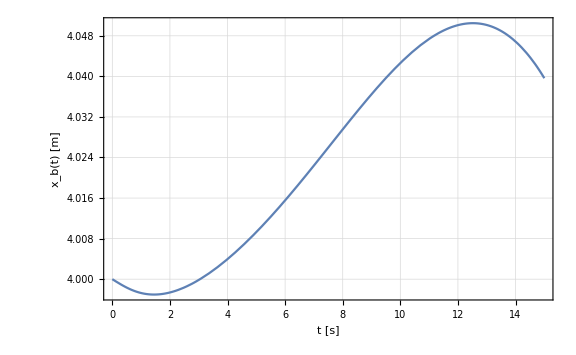
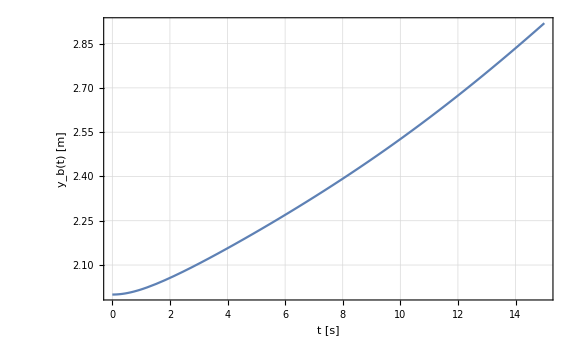
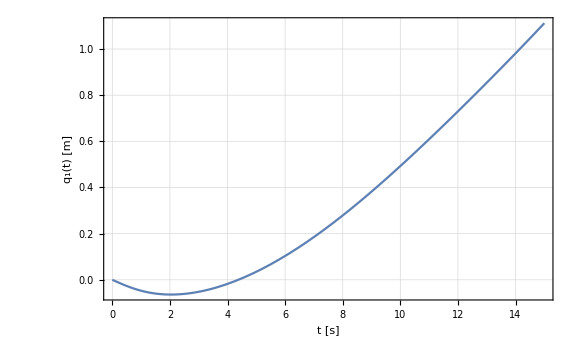
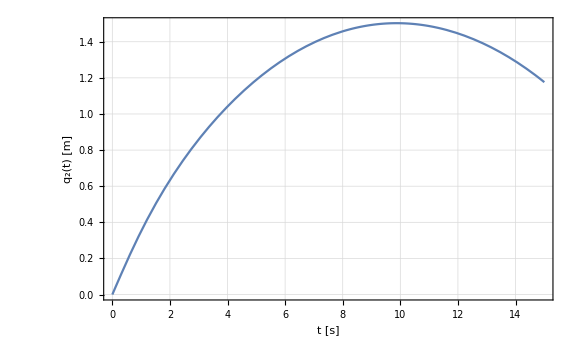
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[2,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[3,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[4,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[5,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

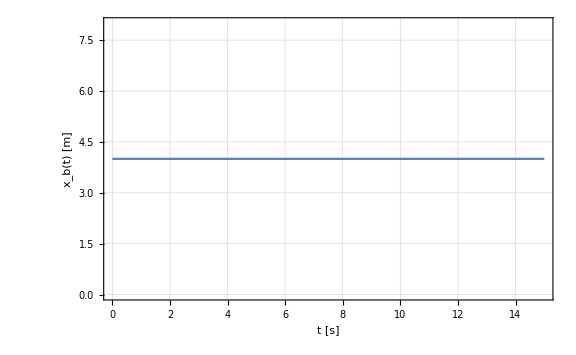
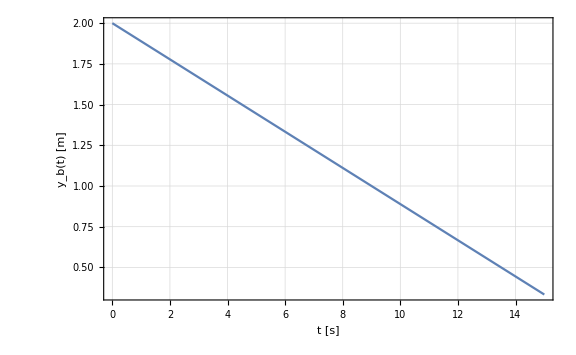
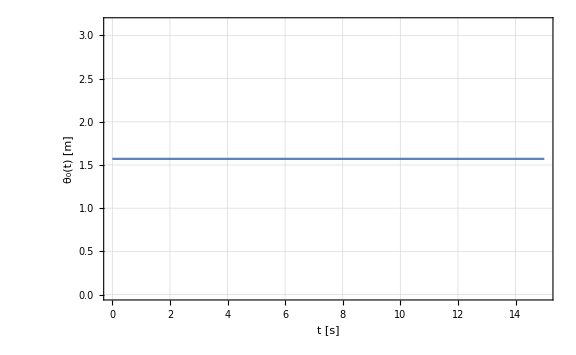
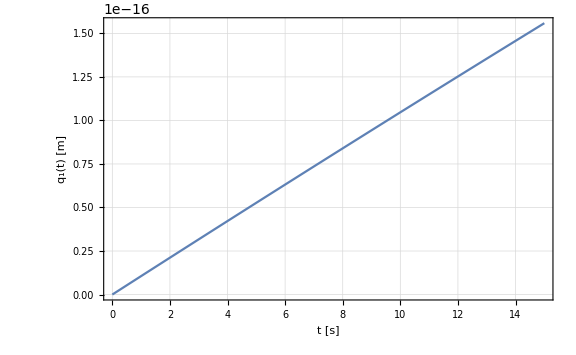
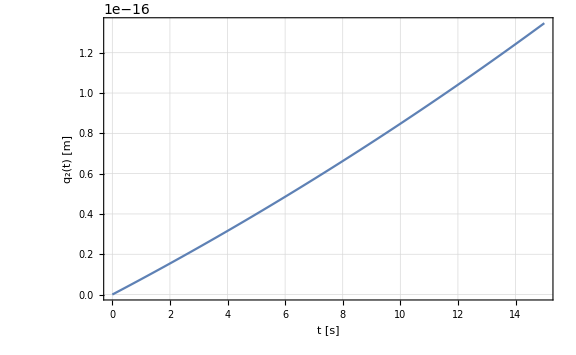

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[2,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[3,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[4,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[5,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotRange->{{0,10},{0,10}},PlotMarkers->{Automatic, 5}];
```

```mathematica
{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10}
{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10}
```

{{4.04263,2.5265},{2.15056,6.05071},{-1.03875,4.60908}}

{{4.,0.888889},{4.,4.88889},{4.,8.38889}}

```mathematica
RobotPlotAfter1=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

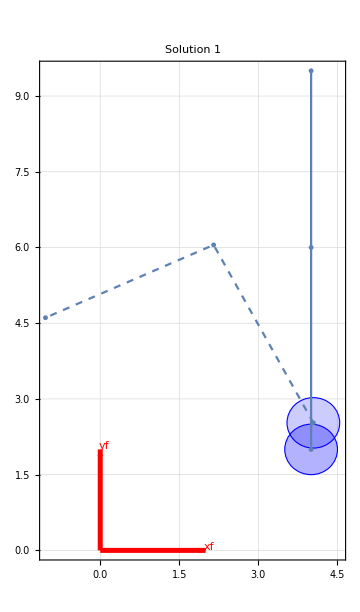
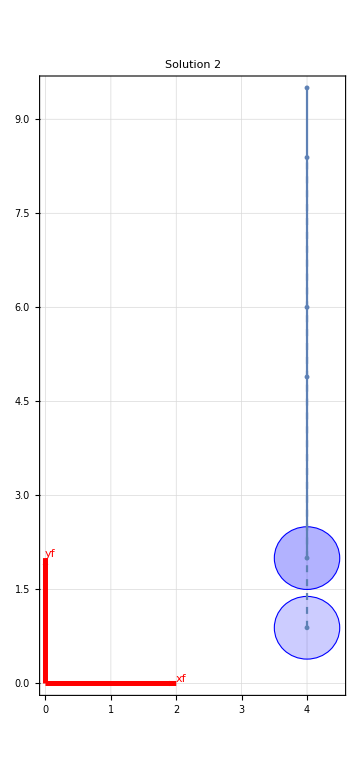

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

### Simulation with control

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=1IdentityMatrix[5];
Kv=2 Sqrt[Kp];
```

```mathematica
pd={xb[t],yb[t],θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0,0,0};
```

{4,2,π/2,0,0}

```mathematica
U=-Mp.(Kv.(p'-pd')+Kp.(p-pd))+Cp;
```

```mathematica
eqMotionControl=Mp.D[p,t,t]+Cp-U;
```

```mathematica
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotionControl2=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

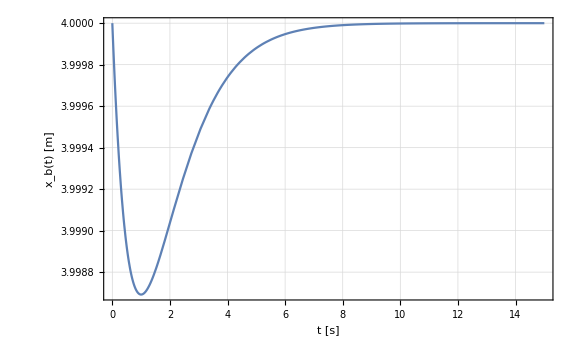
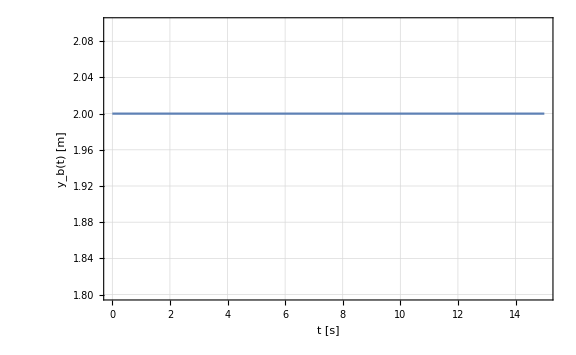
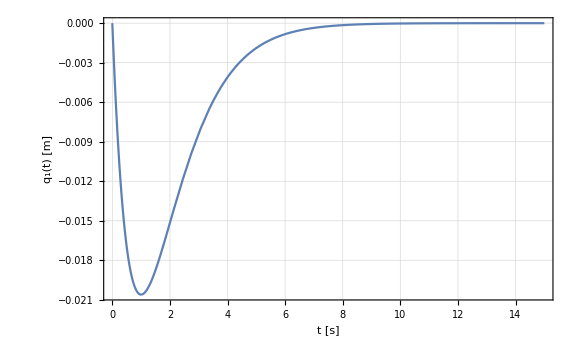
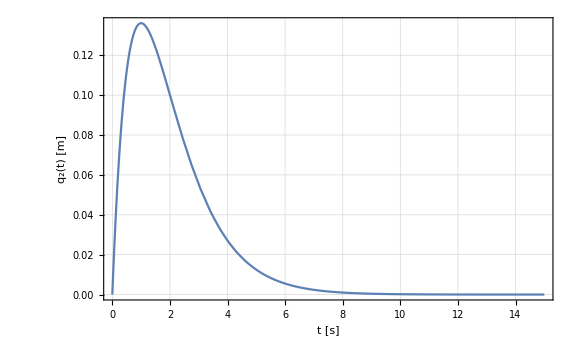
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl1[[1,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[2,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[solMotionControl1[[3,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[4,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[5,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

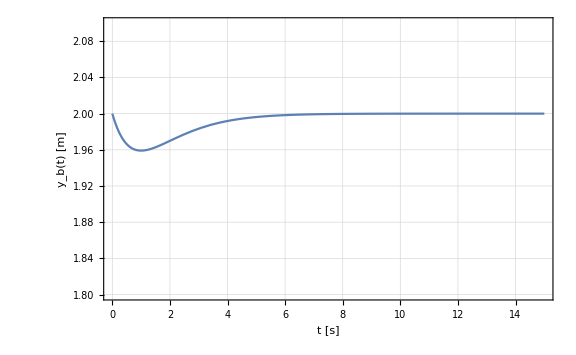
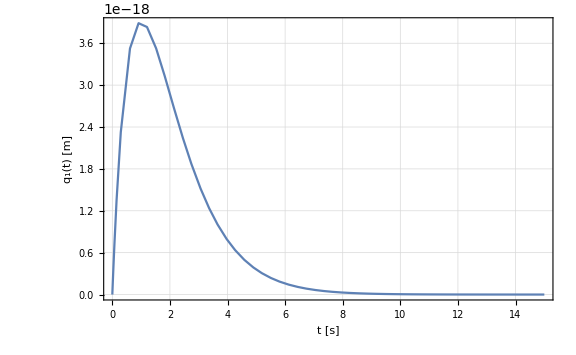
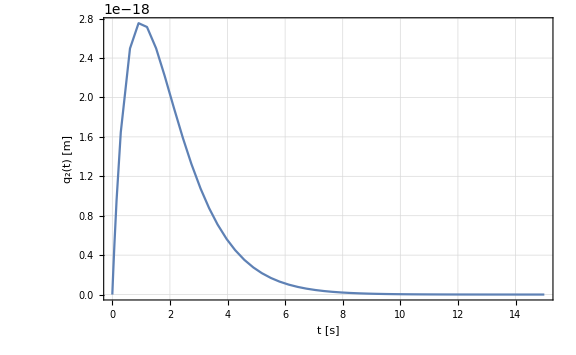
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl2[[1,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[2,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[solMotionControl2[[3,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[4,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[5,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```